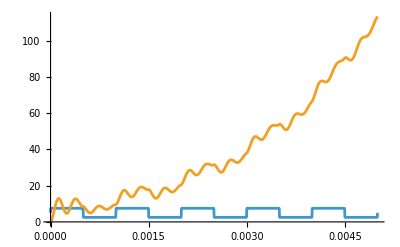

```mathematica
ClearAll["Global`*"];
suciastky={r1->3300,r2->47000,l->22*10^-3,c1->39*10^-9,c2->82*10^-9};
amp=5;
f=1000;
tmax=5*1/f;
uz[t_]:=amp*(1+Tanh[100*Sin[2*Pi*f*t]]/2)
rovnice = 
{

0==il[t]+ir1[t]+ic1[t],
ir1[t]+il[t]==ir2[t]+iu[t],
iu[t]+ic2[t]==0,

uz[t]==u2[t]-u3[t],
u1[t]-u2[t]==r1*ir1[t],
u2[t]==r2*ir2[t],
u1[t]-u2[t]==l*il'[t],
ic1[t]==c1*u1'[t],
ic2[t]==c2*u3'[t],

il[0]==0,
u1[0]==0,
u3[0]==0

};
premenne={u1[t],u2[t],u3[t],iu[t],ir1[t],ir2[t],ic1[t],ic2[t],il[t]};
riesenie=NDSolve[rovnice/.suciastky,premenne,{t,0,tmax}][[1]];
Plot[{uz[t],u3[t]/.riesenie},{t,0,tmax}]
```

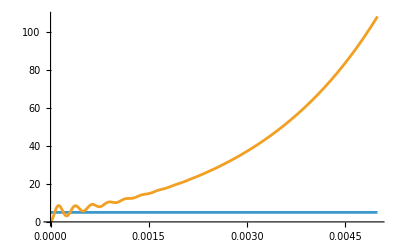

```mathematica
uz[t_]:=5
rovnice = 
{

0==il[t]+ir1[t]+ic1[t],
ir1[t]+il[t]==ir2[t]+iu[t],
iu[t]+ic2[t]==0,

uz[t]==u2[t]-u3[t],
u1[t]-u2[t]==r1*ir1[t],
u2[t]==r2*ir2[t],
u1[t]-u2[t]==l*il'[t],
ic1[t]==c1*u1'[t],
ic2[t]==c2*u3'[t],

il[0]==0,
u1[0]==0,
u3[0]==0

};
premenne={u1[t],u2[t],u3[t],iu[t],ir1[t],ir2[t],ic1[t],ic2[t],il[t]};
riesenie=NDSolve[rovnice/.suciastky,premenne,{t,0,tmax}][[1]];
Plot[{uz[t],u3[t]/.riesenie},{t,0,tmax}]
```